```mathematica
ClearAll["`*"]
Needs["EntropyGO`",NotebookDirectory[]<>"../src/EntropyGO.m"]
```

{{2,3}}

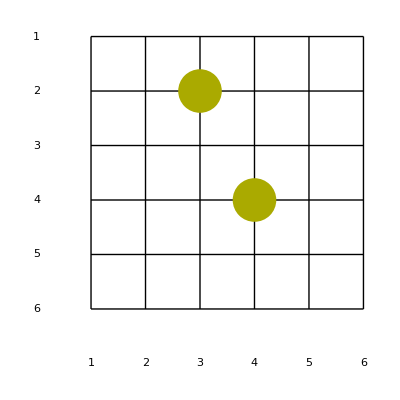

```mathematica
(*subα={GO`Private`α-> α,Abs[GO`Private`α]-> α};*)


Board= {{0,0,0,0,0,0},{0,-1,1,0,-1,0},{0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}};
Board= {{0,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}};
LoadBoard[Board]
Groups[1][[1]]
Draw[]
```

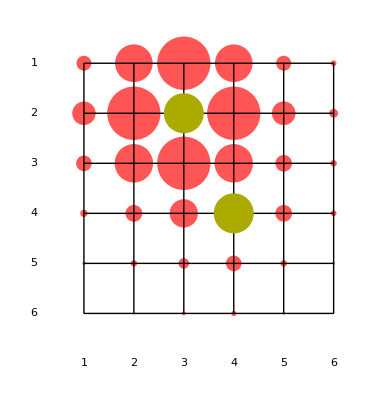

```mathematica
options={"boardPaths"-> True};
{boardInf,boardPaths}= BoardInfluenceFromGroup[Groups[1][[1]],1,options];

boardInf~DrawTentacles~3
```

```mathematica
boardInf
```

{{1.11773,2.82101,4,2.82101,1.12618,0.423183},{1.75561,4,0,4,1.77315,0.657875},{1.17286,2.88103,4,2.88103,1.24724,0.482343},{0.551443,1.25984,2.11913,0,1.25746,0.432352},{0.223277,0.482343,0.791747,1.17286,0.493203,0.195448},{0.0815358,0.174198,0.286623,0.393716,0.189801,0.0767834}}

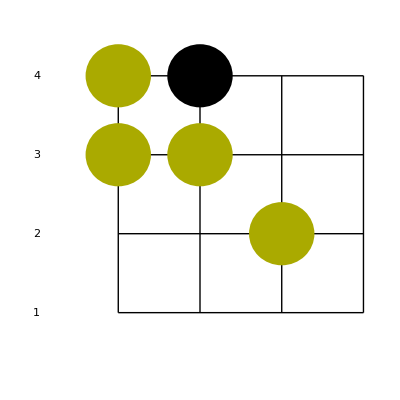

```mathematica
(*All boards need to be square*)
Board= {{0,1,0,-1,0},{0,0,0,0,0},{0,-1,-1,0,0},{0,0,0,0,0},{0,0,0,0,0}};
Board= {{1,-1,0,0},{1,1,0,0},{0,0,1,0},{0,0,0,0}};
LoadBoard[Board]
Draw[]
```

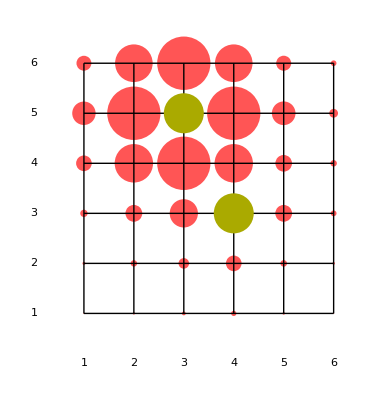

```mathematica
BoardOfLinksUDRL//MatrixForm;
Groups[1];
Groups[-1];

options={"boardPaths"-> True};
Groups[1][[1]];
{boardInf,boardPaths}= BoardInfluenceFromGroup[Groups[1][[1]],1,options];
boardInf~DrawTentacles~3
```

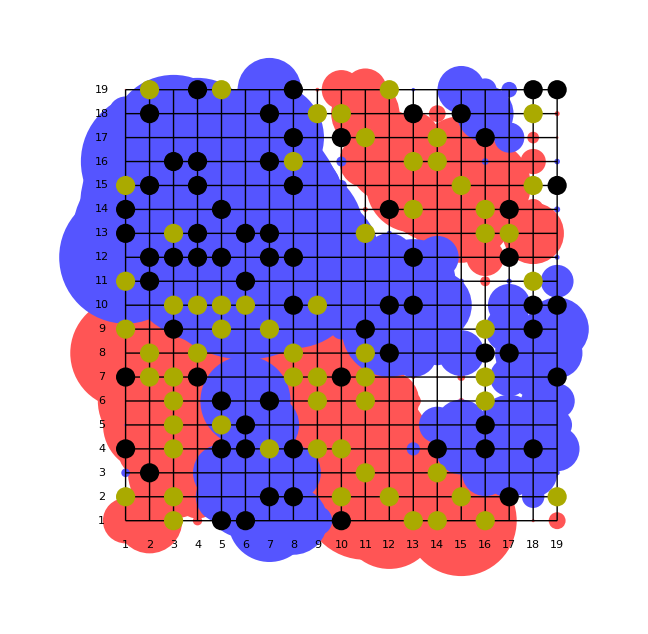

```mathematica
GenerateRandomBoard[19]
BoardInfluence~DrawTentacles~3
Draw[];
(*BoardInfluence  //RuntimeTools`Profile*)
```

```mathematica
(*Compilation attempts*)
ClearAll[AdjacentGroup,CAdjacentGroup]
AdjacentGroup[group_,coord_]:=  Intersection [{#[[1]]}&/@Position[group, Alternatives@@((coord+#)&/@listUDRL),2,4]];
CAdjacentGroup= Compile[{{group,_Integer,3},{coord,_Integer,1} },
  Intersection [{#[[1]]}&/@Flatten[Position[group,#,2,4]&/@(({2,2}+#)&/@listUDRL) ,1]]
];

Timing[AdjacentGroup[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}]][[1]]
Timing[CAdjacentGroup[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}]][[1]]

list[f_]:= Timing[Do[f[{{{3,2}},{{3,3}},{{2,1},{1,2}}},{2,2}];,{#}]][[1]]&/@Range[100,2500,200]
ListPlot[{list[CAdjacentGroup],list[AdjacentGroup]} ]

<<CompiledFunctionTools`
CompilePrint[CAdjacentGroup];
```